```mathematica
(* Evaluate this cell before doing anything else in order to define functions. *)

SetDirectory[NotebookDirectory[]];  (* Sets all path names to be relative to the directory where this notebook is. *)

(* Functions one can calculate on each time frame. *)
p[timeframe_]:=("data"/.timeframe)[[1]]
πp[timeframe_]:=("data"/.timeframe)[[2]]
q[timeframe_]:=("data"/.timeframe)[[3]]
πq[timeframe_]:=("data"/.timeframe)[[4]]
λ[timeframe_]:=("data"/.timeframe)[[5]]
πλ[timeframe_]:=("data"/.timeframe)[[6]]
τ[timeframe_]:=("time"/.timeframe)
α[timeframe_]:=1/(2πλ[timeframe])^2
v[timeframe_]:=p[timeframe]+τ[timeframe]
ρ[timeframe_]:=-1/2 Log[α[timeframe]]
l[timeframe_]:=p[timeframe]+1/2λ[timeframe]-3/2τ[timeframe]-Log[2]
Ptau[timeframe_]:=-πp[timeframe]/(2*πλ[timeframe])
Qtau[timeframe_]:=-Exp[-2p[timeframe]]πq[timeframe]/(2*πλ[timeframe])
λtau[timeframe_]:=1/(2*πλ[timeframe])^2(πp[timeframe]^2+Exp[-2p[timeframe]]πq[timeframe]^2+Exp[-2τ[timeframe]]spacederivative[p,timeframe]^2+Exp[2(p[timeframe]-τ[timeframe])]spacederivative[q,timeframe]^2)+Exp[(λ[timeframe]+2p[timeframe]+3τ[timeframe])/2]
Vtau[timeframe_]:=Ptau[timeframe]+1
ρtau[timeframe_]:=Exp[l[timeframe]]
A[timeframe_]:=Mean[-πp[timeframe]+2πλ[timeframe]+q[timeframe]*πq[timeframe]];
B[timeframe_]:=Mean[-πq[timeframe]];
c[tf_]:=Mean[(Qtau[tf]-2q[tf]+q[tf]Vtau[tf])2 πλ[tf]+q[tf](-πp[tf]+2πλ[tf]+q[tf]*πq[tf])];

(* Computes a finite-difference spatial derivative of a function on a time frame. *)
spacederivative=
Function[{f,timeframe},
Module[{temp,n,Δx},
temp=f[timeframe];
n=Length[temp];
Δx=2 Pi / n;
temp=Join[
{temp[[n-1]]},
{temp[[n]]},
temp,
{temp[[1]]},
{temp[[2]]}
];
Table[(2/3*(temp[[i+1]]-temp[[i-1]])+1/12*(temp[[i-2]]-temp[[i+2]]))/Δx,{i,1+2,n+2}]
]
];

(* Calculate the constraint. Note that this is pointwise in space. This should be identically 0 for solutions without error. *)
galconstraint[tf_]:=Module[{dp,dq,dλ},
 dp=spacederivative[p,tf];
 dq=spacederivative[q,tf];
 dλ=spacederivative[λ,tf];
(dp*πp[tf])+(dq*πq[tf])+(dλ*πλ[tf])
]
galconstraintavg[tf_]:=Mean[galconstraint[tf]]

(* More functions that can be computed on time frames. *)
Ev[tf_]:=Vtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[p,tf]^2
Eq[tf_]:=Exp[2(v[tf]-τ[tf])](Qtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[q,tf]^2)
En[tf_]:=Ev[tf]+Eq[tf]
J[tf_]:=1/2 En[tf]
mE[tf_]:=Mean[Exp[ρ[tf]-2τ[tf]] J[tf]]
Π[tf_]:=Mean[Exp[ρ[tf]] ]
Λ[tf_]:=1/2Mean[Exp[-2τ[tf]+ρ[tf]]Vtau[tf](v[tf]-Mean[v[tf]]-1)]
H[tf_]:=Π[tf](mE[tf]+Λ[tf])
Y[tf_]:=Mean[Exp[l[tf]+ρ[tf]+2τ[tf]]]
cc[tf_]:=Π[tf]Exp[-τ[tf]]H[tf]^(-1/2)
dd[tf_]:=Y[tf]Exp[-3τ[tf]]H[tf]^(-1/2)

ltau[tf_]:=-2-ρtau[tf]+1/2En[tf]

(* The terms from Beverly's superhamiltonian. The 'a' versions below just have an extra factor of 1/πλ so that they are O(1) generically. *)
H0[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe])
Hkin[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf])
Hsmall[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf])
Hcurv[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf])
Htwist[tf_]:=πλ[tf] Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]

H0a[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe]*πλ[timeframe])
Hkina[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf]*πλ[tf])
Hsmalla[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf]*πλ[tf])
Hcurva[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf]*πλ[tf])
Htwista[tf_]:= Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]

(* This is the function that takes a path to a json file and turns the result into a Mathematica-friendly form. DO NOT USE THIS FUNCTION DIRECTLY. Use the function apnp defined below instead. *)
myimport[path_]:=Block[{text,timeframes},
(* There is a bug with importing json floats of length greater than 19. See https://mathematica.stackexchange.com/questions/163825/problem-to-import-numbers-longer-than-19-digit-with-json-or-rawjson *)
Import[path,"Text"]//StringReplace[{"{"->"<|","}"->"|>",":"->"->","["->"{","]"->"}","e+"~~s_:>" 10^"~~s,"e-"~~s_:>" 10^-"~~s}]//ToExpression
]

(* Returns a nice (x,y) table after applying the function f to all the time frames. *)
ClearAll[pairs];
pairs[file_,f_]:=Block[{data,timeframes},
data=file//myimport;
 (* +++++++++++++++++++++++++++++++++++++
NOTA BENE: I use the operator // a lot in my coding.
The meaning is this: x//f//g == g[f[x]] analogous to the pipe | in *nix shells.
Closely related is the /* operator: f/*g is the function which is the composition of f and g.
That is, (f/*g)[x] = g[f[x]].
The difference is that f/*g can be passed around as a function, while f//g cannot; the latter must be applied to some input.
+++++++++++++++++++++++++++++++++++++ *)
timeframes=("evolution"/.data);
Table[{τ[i],f[i]},{i,timeframes}]//Sort[#,#1[[1]]<#2[[1]]&]&
]

(* Return a list of all the json files in the same directory as the input. *)
files=Function[file,
Module[{root,dir},
dir=DirectoryName[file];
root=FileBaseName[file];
FileNames[root<>".*.json",{dir}]
]
];

(*$HistoryLength=0;*)

(* The next few functions are related to actually getting data out of json files. Part of the complexity is related to memoization. There is the logic: 
  1) myimport gets data from a file and returns it as an array, but it doesn't memoize what is returned, so if we keep re-evaluating the same function on the same file, it takes the time to read the file from disk each time.
  2) pairshm is a memoized version of myimport: if we call it on the same file with the same function, it doesn't read the file again. The line <<"pairshm.mx"; reads previously memoized values from a file when we open the notebook again.
  3) The underlying files might change (as we evaluate for longer times) so we want to load them anew if they have changed, so pairsm gets the size and date of the file and makes pairshm get it again if these values have chaged.
  4) All the previous functions only act on a single file, but the data may be split up between many files. The function apnp looks for other files in the same directory for the given run and loads the data for all of them, then combines it and sorts by time. This is the function you should actually call to get a list of time frames.
*)

ClearAll[pairshm];
<<"pairshm.mx";
pairshm[file_,f_,size_,date_]:=pairshm[file,f,size,date]=Block[{data,timeframes},
PrintTemporary[file];
pairshm//DownValues//Map[#[[1]]&]//Select[StringMatchQ[ToString[#],___~~file~~___]&]//Select[StringMatchQ[ToString[#],___~~ToString[f]~~___]&]//Map[(#=.)&]; (* Clear previous memoizations for this function and file if they exist. *)
data=file//myimport;
timeframes=("evolution"/.data);
Table[{τ[i],f[i]},{i,timeframes}]
]

ClearAll[pairsm];
pairsm[file_,f_]:=pairshm[file,f,file//FileByteCount,file//FileDate//UnixTime];

files2=Function[file,
Module[{root,dir,reses,filenames},
dir=DirectoryName[file];
root=FileBaseName[file];
filenames=FileNames[root<>"_*.*.json",{dir}];
reses=filenames//Map[StringReplace[__~~"_"~~s__~~"."~~__~~".json":>s]]//Union//SortBy[ToExpression[#]&];
reses//Map[Select[filenames,StringMatchQ[dir~~root~~"_"~~#~~"."~~__~~".json"]]&]
]
];

ClearAll[apnp];
apnp[file_,f_]:=Block[{files,out},
files=files2[file]//Flatten;
out=Table[
j->pairsm[j,f]
,{j,files}]//Flatten[#,1]&;
(files2[file]/.out)//Map[Flatten[#,1]&]//Map[SortBy[#[[1]]&]]
]

dir="../long_runs/"; (* for the notebook, set the location where the runs are stored. *)
resolutions=Range[1,2]; (* Which resolutions to look for. 1 -> 512 , 2 -> 1024 , ... *)
twidth=5; (* When generating tables of plots, how many columns should there be? *)
```

5

{gen_0,gen_3,gen_27,gen_57,gen_59}

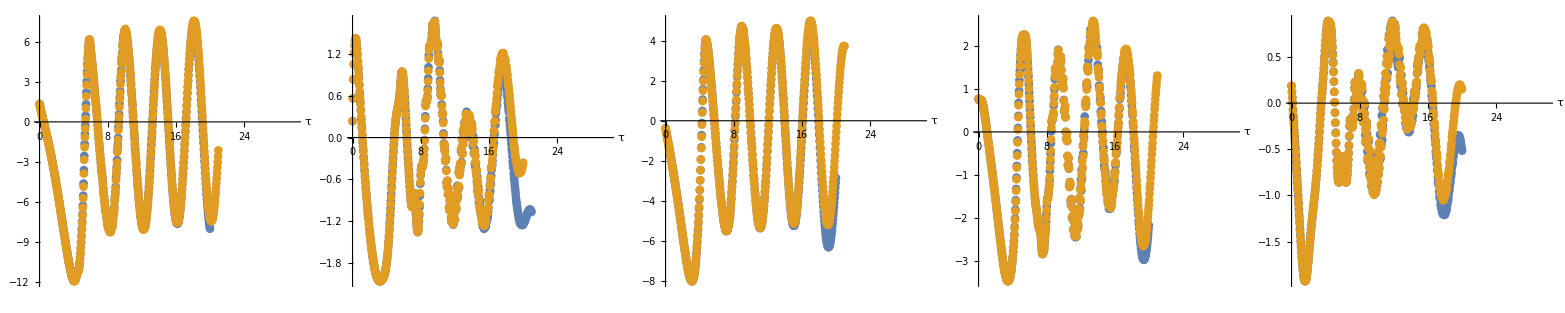

-rw-rw-r-- 1 adam adam 234K Jun  8 15:38 pairshm.mx

```mathematica
Module[{type,filenames,runs,filess,k,print,i},
filenames=FileNames["*t_*.1.json",{dir}];
i=0;
runs=filenames//StringReplace[dir<>"t_"~~typeandnum__~~"_"~~__~~".json"->typeandnum]//Union//SortBy[ToExpression[#]&];
Print[runs//Length];
Print[runs];
Module[{tmp},
tmp=
Monitor[
Table[  (* For each run... *)
{
filee
,apnp[  (* ... get all the data from all the files ... *)
dir<>"t_"<>filee<>".json"
,{
galconstraint/*Abs/*Max/*Log10
,1/Π[#]Mean[Exp[ρ[#]]Ev[#]]&
,1/Π[#]Mean[Exp[ρ[#]]Eq[#]]&
,Mean[(l[#]-Log[1/2])]Exp[τ[#]/4]&
,Mean[(ρ[#]-τ[#]/2)Exp[ρ[#]]]/Mean[Exp[ρ[#]]]&
}[[4]] (* ... and apply the function I select from this little list ... *)
]//ListPlot[  (* ... then plot it ... *)
#[[resolutions]]
,PlotRange->{{0,30},All}
,PlotStyle->PointSize[1/64]
,ImageSize->Scaled[1/twidth ]
,Epilog->Inset[Framed[filee,Background->LightYellow],ImageScaled[{.8,.2}]] (* ... with a nice label of the name of the run ... *)
,AxesLabel->{"τ",""}
]&
}
,{filee,runs}
]
,{ProgressIndicator[FirstPosition[runs,filee][[1]]-1,{0,runs//Length},ImageSize->Scaled[1/2]],filee}];(*
tmp//Map[Export[#[[1]]<>"_rho.png",#[[2]],ImageSize->1000]&];*) (* uncomment the stuff to the left if you'd like to write images of the plots to the disk. *)
tmp//Map[#[[2]]&]
]//Partition[#,UpTo[twidth]]&//TableForm (* ... and make a nice grid of all the plots for the runs. *)
]

Module[{path="pairshm.mx"},
DumpSave[path,pairshm];
RunProcess[{"ls","-lh",path},"StandardOutput"]
]
```

```mathematica
genericruns512={"gen_0","gen_3","gen_27","gen_57","gen_59","gen_71","gen_87","gen_95","gen_97","gen_130","gen_138","gen_148","gen_154","gen_157","gen_159","gen_164","gen_191"}//Map[getfullrun[#,"512"]&,#,{1}]&;
```

```mathematica
DumpSave["/media/adam/mobile storage/ha/data2_100/genericruns512.mx",genericruns512];
RunProcess[{"ls","-lh","/media/adam/mobile storage/ha/data2_100/genericruns512.mx"},"StandardOutput"]
```

-rw-rw-rw- 1 adam adam 1,7G feb 24 22:08 /media/adam/mobile storage/ha/data2_100/genericruns1024.mx

```mathematica
genericruns4096[[2]][[;;;;16]]//Function[bulk,
ρ∞=ρ[bulk[[-1]]]-τ[bulk[[-1]]]/2;
Map[
Function[frame,
Module[{length,tempdata,time,t},
time=frame//τ;
t=Exp[time/2];

tempdata=frame//(
J[#]
)&;
length=tempdata//Length;
Table[{time,2Pi(i-1)/length,tempdata[[i]]},{i,1,length}]
]
]
,bulk]]//Flatten[#,1]&//Show[
ListPlot3D[#,PlotRange->All,ImageSize->Scaled[1],BoxRatios->{3, 1, 1}]
]&
```

```mathematica
genericruns4096[[2]][[-800;;;;2]]//Function[bulk,
l∞=Log[1/2];
Map[
Function[frame,
Module[{length,tempdata,time,t},
time=frame//τ;
t=Exp[time/2];

tempdata=frame//(
Exp[time/4](Exp[time/4](l[#]-l∞)-Mean[Exp[time/4](l[#]-l∞)])
)&;
length=tempdata//Length;
Table[{t,2Pi(i-1)/length,tempdata[[i]]},{i,1,length}]
]
]
,bulk]]//Flatten[#,1]&//Show[
ListPlot3D[#,PlotRange->All,ImageSize->Scaled[1],BoxRatios->{3, 1, 1}]
]&
```

```mathematica
displotsgen[data_,name_]:=Block[{plot,n,path,temp,a,pdfize,fit,ffit,ddata},
(*
pdfize[string_]:=ExportString[string,"PDF"]//ImportString[#]&//#[[1]]&//Show[#,ImageSize->20]&;
*)
fit[ddata_]:=Module[{lastnth,model,parameters},
lastnth[l_,nn_]:=l[[-Round[Length[l]/nn];;]];
model=b(*+h x*)+  e Sin[ f ( x + g)];
parameters=ddata//lastnth[#,2^2]&//FindFit[#,model,{b,e,f,g(*,h*)},x,MaxIterations->1000,Method->NMinimize]&;
model/.parameters
];
(*
ddata={
F[data,{τ,1/Π[#]*Mean[ Ev[#]Exp[ρ[#]]]&},0]
,F[data,{τ,1/Π[#]*Mean[ Eq[#]Exp[ρ[#]]]&},0]
,F[data,{τ,1/Π[#]*Mean[(Ev[#]+Eq[#])Exp[ρ[#]]]&},0]
};*)
l∞=Mean[l[data[[-1,2]]]];
ddata={
F[data,{τ,Exp[τ[#]/4]Max[Abs[l[#]-l∞]]&},0]
};
(*
ffit=fit[ddata[[1]]];*)

plot=
Show[
ddata//ListLinePlot[#
,PlotRange->{{All,All},All}
,AxesLabel->{"τ",""}(*
,PlotLabels->Map[pdfize,{"E_V","E_Q","E"}]*)
,PlotStyle->{{Black,Dashing[0.02],Thickness[0.006]},{Black,Dotted,Thickness[0.006]},{Black,Thickness[0.006]}}
,InterpolationOrder->2
,Epilog->{
Inset[Framed[name,Background->White],ImageScaled[{.2,.2}]](*
,Inset[Framed[SetPrecision[ffit,3],Background->White],ImageScaled[{.7,.2}]]*)
}
]&(*
,ContourPlot[y==5/2,{x,-100,100},{y,-100,100},ContourStyle->{Thick,Red}]*)(*
,Plot[ffit,{x,-10,40},PlotStyle->{Thick,Purple}]*)
];
path="/tmp/tmp.JAbY0fYRhY/"<>name;(*
plot//Style[#,AutoStyleOptions->{"HighlightFormattingErrors"->False}]&//Export[path<>"_e.pdf",#,ImageSize->Scaled[2],"AllowRasterization"->False]&;*)
plot
]

Table[
genericruns4096[[i,-1600;;;;1]]//displotsgen[Map[{τ[#],#}&,#],genericrunsnames[[i]]]&
,{i,1,Min[Infinity,genericruns4096//Length]}]//Partition[#,UpTo[5]]&//GraphicsGrid[#,ImageSize->Scaled[1]]&
```

```mathematica
displotsgen[data_,name_]:=Block[{plot,n,path,temp,a,pdfize,fit,ffit,ddata},
(*
pdfize[string_]:=ExportString[string,"PDF"]//ImportString[#]&//#[[1]]&//Show[#,ImageSize->20]&;
*)
fit[ddata_]:=Module[{lastnth,model,parameters},
lastnth[l_,nn_]:=l[[-Round[Length[l]/nn];;]];
model=b(*+h x*)+  e Sin[ f ( x + g)];
parameters=ddata//lastnth[#,2^2]&//FindFit[#,model,{b,e,f,g(*,h*)},x,MaxIterations->1000,Method->NMinimize]&;
model/.parameters
];
(*
ddata={
F[data,{τ,1/Π[#]*Mean[ Ev[#]Exp[ρ[#]]]&},0]
,F[data,{τ,1/Π[#]*Mean[ Eq[#]Exp[ρ[#]]]&},0]
,F[data,{τ,1/Π[#]*Mean[(Ev[#]+Eq[#])Exp[ρ[#]]]&},0]
};*)
(*
ddata={
F[data,{τ,Exp[τ[#]/4]Mean[ ρ[#]-τ[#]/2-(ρ[data[[-1,2]]]-τ[data[[-1,2]]]/2)]&},0]
};*)

ddata={
F[data,{τ,Exp[τ[#]/4](1/Π[#]*Mean[ ltau[#]Exp[ρ[#]]])&},0]
};

ffit=fit[ddata[[1]]];

plot=
Show[
ddata//ListLinePlot[#
,PlotRange->{{All,All},All}
,AxesLabel->{"τ",""}(*
,PlotLabels->Map[pdfize,{"E_V","E_Q","E"}]*)
,PlotStyle->{{Black,Dashing[0.02],Thickness[0.006]},{Black,Dotted,Thickness[0.006]},{Black,Thickness[0.006]}}
,InterpolationOrder->2
,Epilog->{
Inset[Framed[name,Background->White],ImageScaled[{.2,.2}]]
,Inset[Framed[SetPrecision[ffit,3],Background->White],ImageScaled[{.7,.2}]]}
]&(*
,ContourPlot[y==5/2,{x,-100,100},{y,-100,100},ContourStyle->{Thick,Red}]*)
,Plot[ffit,{x,-10,40},PlotStyle->{Thick,Purple}]
];
path="/tmp/tmp.JAbY0fYRhY/"<>name;(*
plot//Style[#,AutoStyleOptions->{"HighlightFormattingErrors"->False}]&//Export[path<>"_e.pdf",#,ImageSize->Scaled[2],"AllowRasterization"->False]&;*)
plot
]

Table[
genericruns1024[[i,-2000;;;;16]]//displotsgen[Map[{τ[#],#}&,#],genericrunsnames[[i]]]&
,{i,1,Min[Infinity,genericruns4096//Length]}]//Partition[#,UpTo[5]]&//GraphicsGrid[#,ImageSize->Scaled[1]]&
```

```mathematica
Pi/2//N
```

1.5708

```mathematica
displotsgen[data_,name_]:=Block[{plot,n,path,temp,a,pdfize,fit,ffit,ddata},
(*
pdfize[string_]:=ExportString[string,"PDF"]//ImportString[#]&//#[[1]]&//Show[#,ImageSize->20]&;
*)(*
fit[ddata_]:=Module[{lastnth,model,parameters},
lastnth[l_,nn_]:=l[[-Round[Length[l]/nn];;]];
model=b+  e Sin[ f ( x + g)];
parameters=ddata//lastnth[#,2^2]&//FindFit[#,model,{b,e,f,g},x,MaxIterations->1000,Method->NMinimize]&;
model/.parameters
];
*)
ddata={
F[data[[2;;]],{τ,Mean[λ[#]-4τ[#]]&},0](*
,F[data,{τ,1/Π[#]*Mean[ Eq[#]Exp[ρ[#]]]&},0]
,F[data,{τ,1/Π[#]*Mean[(Ev[#]+Eq[#])Exp[ρ[#]]]&},0]*)
};
(*
ffit=fit[ddata[[1]]];
*)
plot=
Show[
ddata//ListLinePlot[#
,PlotRange->All
,AxesLabel->{"τ",""}(*(*
,PlotLabels->Map[pdfize,{"E_V","E_Q","E"}]*)
,PlotStyle->{{Black,Dashing[0.02],Thickness[0.006]},{Black,Dotted,Thickness[0.006]},{Black,Thickness[0.006]}}*)
,InterpolationOrder->2
,Epilog->{
Inset[Framed[name,Background->White],ImageScaled[{.2,.2}]](*
,Inset[Framed[SetPrecision[ffit,2],Background->White],ImageScaled[{.7,.2}]]*)
}
]&(*
,ContourPlot[y==5/2,{x,-100,100},{y,-100,100},ContourStyle->{Thick,Red}]
,Plot[ffit,{x,-10,40},PlotStyle->{Thick,Purple}]*)
];(*
path="/tmp/tmp.JAbY0fYRhY/"<>name;
plot//Style[#,AutoStyleOptions->{"HighlightFormattingErrors"->False}]&//Export[path<>"_e.pdf",#,ImageSize->Scaled[2],"AllowRasterization"->False]&;*)
plot
]

Table[
genericruns[[i,;;;;128]]//displotsgen[Map[{τ[#],#}&,#],genericrunsnames[[i]]]&
,{i,1,Min[10,genericruns//Length]}]//Partition[#,UpTo[5]]&//GraphicsGrid[#,ImageSize->Scaled[1]]&
```

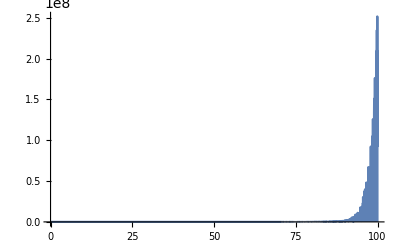
{-Graphics-,(ⅇ^ⅇ π^2)/2}

```mathematica
Module[{V∞,R,guess,model},
V∞:=Exp[1];
R:=Pi;
model=Exp[V∞+1/2t+ Exp[-t/4]R];
guess=Exp[V∞]Exp[t /2]+R Exp[V∞]Exp[t/4];
{
Plot[(model-guess),{t,0,100},PlotRange->{{0,All},{0,All}}],
Limit[(model-guess),t->Infinity]}
]
```

```mathematica
Limit[((Exp[-(V∞+1/2t+ Exp[-t/4]R)])-(ⅇ^(-V∞) Exp[-t /2]-ⅇ^(-V∞) R Exp[-3t/4]+0(ⅇ^(V∞) R^2)/2))Exp[t ],t->Infinity]//Simplify[#,Assumptions->{R∈Reals,V∞∈Reals}]&
```

1/2 ⅇ^(-V∞) R^2

```mathematica
plt[data_,f_]:=data//Map[{τ[#],
f[#]
}&]//ListPlot[#,PlotRange->{{0,20},All},AxesLabel->{Style["τ",15],Style["energy",15]},ImageSize->Scaled[1/3/2]]&
tmp=runs//Map[Function[data,plt[data,Function[frame,
Exp[τ[frame] ]Mean[Exp[ρ[frame]]]Mean[Exp[ρ[frame]-2τ[frame]]1/2(Ev[frame]+Eq[frame])]
]]],#,{2}]&//Transpose//TableForm[{{"generic","b=0","polarised"}}~Join~#]&
(*Export["/home/adam/Dropbox/Documents/research/galileo numerics/rhoplts.png",tmp,ImageSize->1000]*)
```

```mathematica
Exp[k]
```

ⅇ^k

```mathematica
tmp=runs//Map[Function[data,
Show[
plt[data,Function[frame,
1/Π[frame]Mean[Exp[ρ[frame]](Ev[frame]+Eq[frame])]
]]
,Plot[5,{x,-10,100},PlotStyle->{Thick,Red}]
]
],#,{2}]&//Transpose//TableForm[{{"generic","b=0","polarised"}}~Join~#]&
(*Export["/home/adam/Dropbox/Documents/research/galileo numerics/rhoplts.png",tmp,ImageSize->1000]*)
```

```mathematica
tmp=runs//Map[Function[data,
Show[
plt[data,Function[frame,
1/Π[frame]Mean[Exp[ρ[frame]](Ev[frame](*+Eq[frame]*))]
]]
,Plot[5/2,{x,-10,100},PlotStyle->{Thick,Red}]
]
],#,{2}]&//Transpose//TableForm[{{"generic","b=0","polarised"}}~Join~#]&
(*Export["/home/adam/Dropbox/Documents/research/galileo numerics/rhoplts.png",tmp,ImageSize->1000]*)
```

```mathematica
tmp=runs//Map[Function[data,
Show[
plt[data,Function[frame,
1/Π[frame]Mean[Exp[ρ[frame]]((*Ev[frame]+*)Eq[frame])]
]]
,Plot[5/2,{x,-10,100},PlotStyle->{Thick,Red}]
]
],#,{2}]&//Transpose//TableForm[{{"generic","b=0","polarised"}}~Join~#]&
(*Export["/home/adam/Dropbox/Documents/research/galileo numerics/rhoplts.png",tmp,ImageSize->1000]*)
```

```mathematica
runs//Map[
Function[data,
plt[data,
Function[frame,
Mean[Exp[ρ[frame]-τ[frame]/2]1/2(Ev[frame](*+Eq[frame]*))]
]
]
],#,{2}]&
```

3.89601-0.406262 Sin[0.965298 (10.3304+x)]

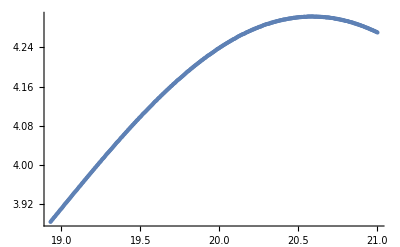

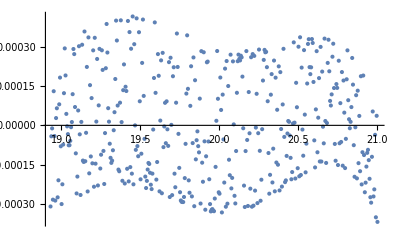

```mathematica
secondhalf[l_]:=l[[Round[Length[l]/2];;]]
lasttenth[l_]:=l[[-Round[Length[l]/10];;]]
data=runs[[1,1]]//Map[
{τ[#],Mean[Exp[ρ[#]-τ[#]/2]1/2(Ev[#](*+Eq[#]*))]}&
,#,{1}]&//lasttenth;
model=a +  e Sin[ f ( x + g)];
parameters=FindFit[data,model,{a,e,f,g},x,MaxIterations->1000,Method->NMinimize];
fit=model/.parameters
maxinput=data//Map[#[[1]]&]//Max;
mininput=data//Map[#[[1]]&]//Min;
Show[
ListPlot[data]
,Plot[fit,{x,mininput,maxinput}]
]
data//Map[{#[[1]],#[[2]]-(fit/.x->#[[1]])}&]//ListPlot
```

```mathematica
1/0.9656631619062923
```

1.03556

```mathematica
plotwithfit[data_]:=Module[{lastnth,dat2,dat,model,parameters,fit,mininput,maxinput},
lastnth[l_,n_]:=l[[-Round[Length[l]/n];;]];
dat2=data//Map[
{τ[#],1/Π[#]Mean[Exp[ρ[#]](Ev[#](*+Eq[#]*))]}&
,#,{1}]&;
dat=dat2//lastnth[#,2^2]&;
model=a +  e Sin[ f ( x + g)];
parameters=FindFit[dat,model,{a,e,f,g},x,MaxIterations->1000,Method->NMinimize];
fit=model/.parameters;
Print[fit];
{mininput,maxinput}=data//Map[τ]//{Min[#],Max[#]}&;
Show[
ListPlot[dat2,ImageSize->Scaled[1]]
,Plot[fit,{x,mininput,maxinput},PlotStyle->{Thick,Red}]
]
]
runs[[1,1]]//plotwithfit
```

2.50001+0.26019 Sin[1.00405 (-0.191395+x)]

```mathematica
<<"/media/adam/mobile storage/ha/data2_100/genericruns.mx"
```

```mathematica
plotwithfit[data_]:=Module[{lastnth,dat2,dat,model,parameters,fit,mininput,maxinput},
lastnth[l_,n_]:=l[[-Round[Length[l]/n];;]];
dat2=data//Map[
{τ[#],1/Π[#]Mean[Exp[ρ[#]](Ev[#](*+Eq[#]*))]}&
,#,{1}]&;
dat=dat2//lastnth[#,2^2]&;
model=a +  e Sin[ f ( x + g)];
parameters=FindFit[dat,model,{a,e,f,g},x,MaxIterations->1000,Method->NMinimize];
fit=model/.parameters;
Print[fit];
{mininput,maxinput}=data//Map[τ]//{Min[#],Max[#]}&;
Show[
ListPlot[dat2,ImageSize->Scaled[1/2]]
,Plot[fit,{x,mininput,maxinput},PlotStyle->{Thick,Red}]
]
]
genericruns[[1]]//plotwithfit
```

2.50316+0.835486 Sin[0.913383 (2.16272+x)]

```mathematica
plotwithfit[data_]:=Module[{lastnth,dat2,dat,model,parameters,fit,mininput,maxinput},
lastnth[l_,n_]:=l[[-Round[Length[l]/n];;]];
dat2=data//Map[
{τ[#],1/Π[#]Mean[Exp[ρ[#]](Ev[#](*+Eq[#]*))]}&
,#,{1}]&;
dat=dat2//lastnth[#,2^2]&;
model=a +  e Sin[ f ( x + g)];
parameters=FindFit[dat,model,{a,e,f,g},x,MaxIterations->1000,Method->NMinimize];
fit=model/.parameters;
Print[fit];
{mininput,maxinput}=data//Map[τ]//{Min[#],Max[#]}&;
Show[
ListPlot[dat2,ImageSize->Scaled[1]]
,Plot[fit,{x,mininput,maxinput},PlotStyle->{Thick,Red}]
]
]
runs[[1,3]]//plotwithfit
```

2.45766+0.808677 Sin[0.929018 (4.83555+x)]

3.89838-0.396374 Sin[0.999447 (-0.144894+x)]

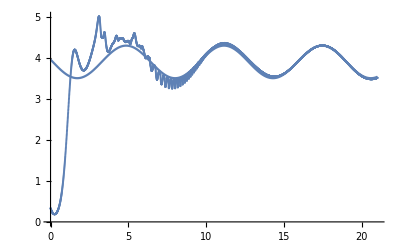

```mathematica
plotwithfit[data_]:=Module[{lastnth,dat2,dat,model,parameters,fit,mininput,maxinput},
lastnth[l_,n_]:=l[[-Round[Length[l]/n];;]];
dat2=data//Map[
{τ[#],Mean[Exp[ρ[#]-τ[#]/2]1/2((*Ev[#]+*)Eq[#])]}&
,#,{1}]&;
dat=dat2//lastnth[#,3]&;
model=a +  e Sin[ f ( x + g)];
parameters=FindFit[dat,model,{a,e,f,g},x,MaxIterations->1000,Method->NMinimize];
fit=model/.parameters;
Print[fit];
{mininput,maxinput}=data//Map[τ]//{Min[#],Max[#]}&;
Show[
ListPlot[dat2]
,Plot[fit,{x,mininput,maxinput}]
]
]
runs[[1,1]]//plotwithfit
```

```mathematica
getfullrunsftp[run_]:=Module[{type},
type=run//StringReplace[s___~~"_"~~__:>s];
ap2["/run/user/1000/gvfs/sftp:host=nuc/media/media/8tbraid/science/ha/9runsdata/t_"~~run~~".json",Identity][[-1]]//Map[#[[2]]&]//MapAt[#[[;;;;2^3]]&,{All,2,All}]//SortBy[τ]
]
```

```mathematica
runs={{"b0_11","b0_59","b0_154"},{"pol_101","pol_102","pol_122"},{"gen_27","gen_59","gen_138"}}//Map[getfullrun,#,{2}]&;
```

```mathematica
runs//Length//Map[Length]
```

```mathematica
DumpSave["/media/adam/mobile storage/ha/data2_100/9runs.mx",runs];
RunProcess[{"ls","-lh","/media/adam/mobile storage/ha/data2_100/9runs.mx"},"StandardOutput"]
```

```mathematica
RunProcess[{"ls","-lh","/run/user/1000/gvfs/sftp:host=nuc/media/media/8tbraid/science/ha/gt/"},"StandardOutput"]
```

```mathematica
FileNames["t_gen_*_512.json",{"/run/user/1000/gvfs/sftp:host=nuc/media/media/8tbraid/science/ha/9runsdata/"}]
```

{/run/user/1000/gvfs/sftp:host=nuc/media/media/8tbraid/science/ha/9runsdata/t_gen_0_512.json,/run/user/1000/gvfs/sftp:host=nuc/media/media/8tbraid/science/ha/9runsdata/t_gen_130_512.json,/run/user/1000/gvfs/sftp:host=nuc/media/media/8tbraid/science/ha/9runsdata/t_gen_138_512.json,/run/user/1000/gvfs/sftp:host=nuc/media/media/8tbraid/science/ha/9runsdata/t_gen_27_512.json,/run/user/1000/gvfs/sftp:host=nuc/media/media/8tbraid/science/ha/9runsdata/t_gen_59_512.json}

```mathematica
plotwithfit[data_]:=Module[{lastnth,dat2,dat,model,parameters,fit,mininput,maxinput},
lastnth[l_,n_]:=l[[-Round[Length[l]/n];;]];
dat2=data//Map[
{τ[#],Exp[τ[#]/4]((Mean[ρ[#]-(ρ[data[[-1]]]-τ[data[[-1]]]/2)])-(τ[#]/2))}&
,#,{1}]&;
dat=dat2//lastnth[#,2^2]&;
model= a3 Sin[f*( x + g)];
parameters=FindFit[dat,model,{a3,f,g},x,MaxIterations->10000,Method->NMinimize];
fit=model/.parameters;
Print[fit];
{mininput,maxinput}=data//Map[τ]//{Min[#],Max[#]}&;
Show[
ListPlot[lastnth[dat2,2]]
,Plot[fit,{x,mininput,2maxinput},PlotStyle->{Thick,Red}]
]
]
runs[[1,2]]//plotwithfit
```

1.51987 Sin[1.61527 (-1.60558+x)]

```mathematica
Log[1/2]//N
```

-0.693147

```mathematica
Pi/2//N
```

1.5708

```mathematica
plotwithfit[data_]:=Module[{lastnth,dat2,dat,model,parameters,fit,mininput,maxinput},
lastnth[l_,n_]:=l[[-Round[Length[l]/n];;]];
dat2=data//Map[
{τ[#],Exp[τ[#]/4]Mean[v[#]-τ[#]/2+0.5790748012757192]}&
,#,{1}]&;
dat=dat2//lastnth[#,4]&;
model=  e Sin[ f ( x + g)];
parameters=FindFit[dat,model,{a,e,f,g},x,MaxIterations->1000,Method->NMinimize];
fit=model/.parameters;
Print[fit];
{mininput,maxinput}=data//Map[τ]//{Min[#],Max[#]}&;
Show[
ListPlot[lastnth[dat2,2]]
,Plot[fit,{x,mininput,maxinput},PlotStyle->{Thick,Red}]
,ImageSize->Scaled[1/2]]
]
runs[[1,2]]//plotwithfit
```

-1.35162 Sin[0.94748 (2.03082+x)]

```mathematica
plotwithfit[data_]:=Module[{lastnth,dat2,dat,model,parameters,fit,mininput,maxinput},
lastnth[l_,n_]:=l[[-Round[Length[l]/n];;]];
dat2=data//Map[
{τ[#],Exp[τ[#]/4]Mean[v[#]-τ[#]/2]}&
,#,{1}]&;
dat=dat2//lastnth[#,4]&;
model=a+  e Sin[ f ( x + g)];
parameters=FindFit[dat,model,{a,e,f,g},x,MaxIterations->1000,Method->NMinimize];
fit=model/.parameters;
Print[fit];
{mininput,maxinput}=data//Map[τ]//{Min[#],Max[#]}&;
Show[
ListPlot[lastnth[dat2,2]]
,Plot[fit,{x,mininput,maxinput},PlotStyle->{Thick,Red}]
,ImageSize->Scaled[1/2]]
]
runs[[1,3]]//plotwithfit
```

-6.84599-4.06777 Sin[0.553085 (4.42098+x)]

```mathematica
plt[data_,f_]:=data//Map[{τ[#],
f[#]
}&]//ListPlot[#,PlotRange->{{0,20},All},AxesLabel->{Style["τ",15],Style["v mean",15]},ImageSize->Scaled[1/3/2]]&
tmp=runs//Map[Function[data,plt[data,Function[frame,
(*Exp[τ[frame] ]Mean[Exp[ρ[frame]]]*)Mean[v[frame]-τ[frame]/2]-Mean[v[data[[-1]]]-τ[data[[-1]]]/2]
]]],#,{2}]&//Transpose//TableForm[{{"generic","b=0","polarised"}}~Join~#]&
(*Export["/home/adam/Dropbox/Documents/research/galileo numerics/rhoplts.png",tmp,ImageSize->1000]*)
```

```mathematica
runs[[1,1]][[-200;;;;10]][[1]]//v//Length
```

512

```mathematica
genericruns4096[[1]]//Length
```

4103

```mathematica
runs[[1,2]][[-2000;;;;2^3]]//Map[
Function[frame,
Module[{length,tempdata,time,t},
time=frame//τ;
t=Exp[time/2];
tempdata=frame//(
Exp[0time/4](Exp[time/4](l[#]-(Log[1/2]))-1(4.860732683220453 Sin[1/2 π (-0.0049708633241589695+time)]))
)&//#[[;;;;2^3]]&;
length=tempdata//Length;
Table[{time,2Pi(i-1)/length,tempdata[[i]]},{i,1,length}]
]
]
]//Flatten[#,1]&//Show[
ListPlot3D[#,PlotRange->All,ImageSize->Scaled[1/3]]
]&
```

```mathematica
runs[[1,3]][[-2000;;;;2^3]]//Map[
Function[frame,
Module[{length,tempdata,time,t},
time=frame//τ;
t=Exp[time/2];
tempdata=frame//(
Exp[time/4](Exp[time/4](l[#]-(Log[1/2]))-(3.126852608114232 Sin[1/2 π (0.40625712710166223+time)]))
)&//#[[;;;;2^3]]&;
length=tempdata//Length;
Table[{time,2Pi(i-1)/length,tempdata[[i]]},{i,1,length}]
]
]
]//Flatten[#,1]&//Show[
ListPlot3D[#,PlotRange->All,ImageSize->Scaled[1]]
]&
```